```mathematica
showArray[arr_]:=Graphics[Raster[(arr-Min[arr])/(Max[arr]-Min[arr])], Frame -> True];
```

```mathematica
makeImage[n_,m_] := 
Table[Sin[x]*Sin[y], {x,0,2Pi}
,{y,0,2Pi}]  ;

showArray[makeImage[20,20]]
```

-Graphics-

Before: -Graphics-

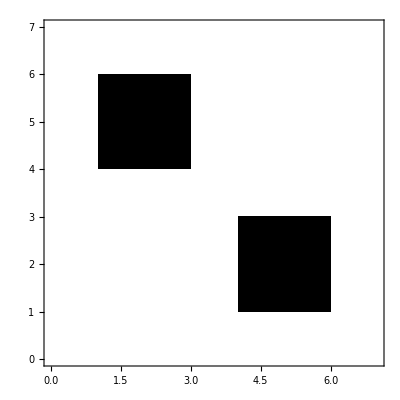
After threshold -1/2: -Graphics-

```mathematica
img1 = makeImage[30,30];
threshold[img_, val_]:=Map[If[#>val,1,0]&,img,{2}];
Print["Before: " , showArray[img1]]
Print["After threshold -1/2: ", showArray[threshold[img1,-1/2]]]
```

```mathematica
blur[img_] := MeanFilter[img,1];
Print["Before: ", showArray[img1]]
Print["After blur: ", showArray[blur[img1]]]
Print["After blur three times: ", showArray[Nest[blur,img1,3]]]
```

Before: -Graphics-

After blur: -Graphics-

After blur*3: -Graphics-